```mathematica
Quit
```

mutilde = input 

btilde = bInput/taap ==> bInput = taap * btilde

---- Check if M5μ makes any difference (Doest not seem so)

----- Check if everything is all right for the small B and small μ 

----- Check if things get better going to even larger ω

## Consider using psub to increase the precision

```mathematica
Timing[Map[Sin[#]&,Range[10^5]]]
Timing[ParallelMap[Sin[#]&,Range[10^5]]]
```

{0.046875,{Sin[1],Sin[2],Sin[3],Sin[4],Sin[5],Sin[6],Sin[7],Sin[8],Sin[9],Sin[10],Sin[11],Sin[12],Sin[13],Sin[14],Sin[15],Sin[16],Sin[17],Sin[18],Sin[19],Sin[20],Sin[21],99959,Sin[99981],Sin[99982],Sin[99983],Sin[99984],Sin[99985],Sin[99986],Sin[99987],Sin[99988],Sin[99989],Sin[99990],Sin[99991],Sin[99992],Sin[99993],Sin[99994],Sin[99995],Sin[99996],Sin[99997],Sin[99998],Sin[99999],Sin[100000]}}
 |  |  |  |

{0.1875,{Sin[1],Sin[2],Sin[3],Sin[4],Sin[5],Sin[6],Sin[7],Sin[8],Sin[9],Sin[10],Sin[11],Sin[12],Sin[13],Sin[14],Sin[15],Sin[16],Sin[17],Sin[18],Sin[19],Sin[20],Sin[21],99959,Sin[99981],Sin[99982],Sin[99983],Sin[99984],Sin[99985],Sin[99986],Sin[99987],Sin[99988],Sin[99989],Sin[99990],Sin[99991],Sin[99992],Sin[99993],Sin[99994],Sin[99995],Sin[99996],Sin[99997],Sin[99998],Sin[99999],Sin[100000]}}
 |  |  |  |

```mathematica
Timing[Map[Sin[#]&,Range[10^6]]]
Timing[ParallelMap[Sin[#]&,Range[10^6]]]
```

{0.375,{Sin[1],Sin[2],Sin[3],Sin[4],Sin[5],Sin[6],Sin[7],Sin[8],Sin[9],Sin[10],Sin[11],Sin[12],Sin[13],Sin[14],Sin[15],Sin[16],Sin[17],Sin[18],Sin[19],Sin[20],999961,Sin[999982],Sin[999983],Sin[999984],Sin[999985],Sin[999986],Sin[999987],Sin[999988],Sin[999989],Sin[999990],Sin[999991],Sin[999992],Sin[999993],Sin[999994],Sin[999995],Sin[999996],Sin[999997],Sin[999998],Sin[999999],Sin[1000000]}}
 |  |  |  |

{1.15625,{Sin[1],Sin[2],Sin[3],Sin[4],Sin[5],Sin[6],Sin[7],Sin[8],Sin[9],Sin[10],Sin[11],Sin[12],Sin[13],Sin[14],Sin[15],Sin[16],Sin[17],Sin[18],Sin[19],Sin[20],999961,Sin[999982],Sin[999983],Sin[999984],Sin[999985],Sin[999986],Sin[999987],Sin[999988],Sin[999989],Sin[999990],Sin[999991],Sin[999992],Sin[999993],Sin[999994],Sin[999995],Sin[999996],Sin[999997],Sin[999998],Sin[999999],Sin[1000000]}}
 |  |  |  |

```mathematica
Timing[Map[Sin[#]&,Range[10^7]]]
Timing[ParallelMap[Sin[#]&,Range[10^7]]]
```

{3.71875,{Sin[1],Sin[2],Sin[3],Sin[4],Sin[5],Sin[6],Sin[7],Sin[8],Sin[9],Sin[10],Sin[11],Sin[12],Sin[13],Sin[14],Sin[15],Sin[16],Sin[17],Sin[18],Sin[19],9999963,Sin[9999983],Sin[9999984],Sin[9999985],Sin[9999986],Sin[9999987],Sin[9999988],Sin[9999989],Sin[9999990],Sin[9999991],Sin[9999992],Sin[9999993],Sin[9999994],Sin[9999995],Sin[9999996],Sin[9999997],Sin[9999998],Sin[9999999],Sin[10000000]}}
 |  |  |  |

{11.2031,{Sin[1],Sin[2],Sin[3],Sin[4],Sin[5],Sin[6],Sin[7],Sin[8],Sin[9],Sin[10],Sin[11],Sin[12],Sin[13],Sin[14],Sin[15],Sin[16],Sin[17],Sin[18],9999964,Sin[9999983],Sin[9999984],Sin[9999985],Sin[9999986],Sin[9999987],Sin[9999988],Sin[9999989],Sin[9999990],Sin[9999991],Sin[9999992],Sin[9999993],Sin[9999994],Sin[9999995],Sin[9999996],Sin[9999997],Sin[9999998],Sin[9999999],Sin[10000000]}}
 |  |  |  |

```mathematica
Timing[Table[Sin[i],{i,10^7}]]
Timing[ParallelTable[Sin[i],{i,10^7}]]
```

{3.01563,{Sin[1],Sin[2],Sin[3],Sin[4],Sin[5],Sin[6],Sin[7],Sin[8],Sin[9],Sin[10],Sin[11],Sin[12],Sin[13],Sin[14],Sin[15],Sin[16],Sin[17],Sin[18],Sin[19],9999963,Sin[9999983],Sin[9999984],Sin[9999985],Sin[9999986],Sin[9999987],Sin[9999988],Sin[9999989],Sin[9999990],Sin[9999991],Sin[9999992],Sin[9999993],Sin[9999994],Sin[9999995],Sin[9999996],Sin[9999997],Sin[9999998],Sin[9999999],Sin[10000000]}}
 |  |  |  |

{13.0625,{Sin[1],Sin[2],Sin[3],Sin[4],Sin[5],Sin[6],Sin[7],Sin[8],Sin[9],Sin[10],Sin[11],Sin[12],Sin[13],Sin[14],Sin[15],Sin[16],Sin[17],Sin[18],Sin[19],9999963,Sin[9999983],Sin[9999984],Sin[9999985],Sin[9999986],Sin[9999987],Sin[9999988],Sin[9999989],Sin[9999990],Sin[9999991],Sin[9999992],Sin[9999993],Sin[9999994],Sin[9999995],Sin[9999996],Sin[9999997],Sin[9999998],Sin[9999999],Sin[10000000]}}
 |  |  |  |

## With M5μ

```mathematica
SetDirectory[NotebookDirectory[]<>"M_derivative"];

mdata11=Get["ω0corrμT100100d10010000d10p6"];
mdata21=Get["ω0corrμT1001000d1002886d10p6"];
```

### M_5

M_5= -1/B 1/k⟨T^tx T^yz(ω=0, k)⟩

```mathematica
M5X[data_]:=-1/B 1/k(*1/bSub[data] 1/kSub[data]*)data⟦All, 3,6⟧
```

```mathematica
M5Xμ[data_]:=Module[{data1=data⟦2,1⟧,data2=data⟦2,2⟧},(M5X[data2]-M5X[data1])/(μSub[data2]-μSub[data1]) ]
```

```mathematica
-(1/10)^-1 10^8(mdata11⟦2,1⟧⟦3,6⟧-mdata11⟦2,2⟧⟦3,6⟧)/10^-10//Im
-(1/10)^-1 10^8(mdata11⟦2,1⟧⟦4,5⟧-mdata11⟦2,2⟧⟦4,5⟧)/10^-10//Im
```

0.01366661608244486011446560349180852356187898521966

-0.01366661608244486011446560349180852356187898521966

```mathematica
-(1443/500000)^-1 10^8(mdata21⟦2,1⟧⟦3,6⟧-mdata21⟦2,2⟧⟦3,6⟧)/10^-10//Im
-(1443/500000)^-1 10^8(mdata21⟦2,1⟧⟦4,5⟧-mdata21⟦2,2⟧⟦4,5⟧)/10^-10//Im
```

-0.05522586138048777936626896637541422923789496579644

0.05522586138048777936626896637541422923789496579644

```mathematica
ρPX[data_,M5μ_]:=bSub[data]^2/(w0[data](w0[data]-bSub[data]^2 M5μ))(all[data]⟦All,3,3⟧)/ωAxis[data]
ρPTX[data_,M5μ_]:=-bSub[data]^2/(w0[data](w0[data]-bSub[data]^2 M5μ))(all[data]⟦All,3,4⟧)/ωAxis[data]
```

```mathematica
-ρPX[data11,0.01367]^-1//Im
```

{0.262229,0.260926,0.260589,0.261069,0.262452,0.265301,0.270412,0.278805,0.291755,0.310856,0.33809,0.375883,0.427073,0.494687,0.581347,0.688254,0.813963,0.953776,1.10073,1.2482,1.39248,1.53361,1.67419,1.81746,1.96593,2.12079,2.28214,2.44943,2.62192,2.79903,2.98036,3.16568,3.35486,3.54776,3.74423,3.94407,4.14708,4.35307,4.56181,4.7731,4.98672,5.20246,5.4201,5.63942,5.86021,6.08222,6.30526,6.52908,6.75347,6.9782}

```mathematica
w0[data21]
```

5.3072741787639529616142118204979674457909212248675790676116

```mathematica
230087
```

be careful. Imaginary value of M_5 also might be contributing to the real value of the shear viscosity. And also in σ

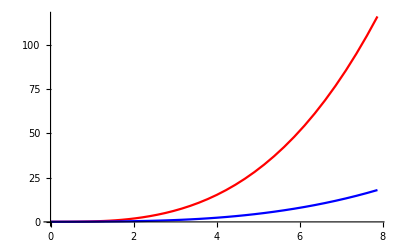

```mathematica
ListPlot[{ωAxis[data11]/(2π taap[data11]),ηPX[data11,-10^10]/entropy[data11]//Im}//Transpose,Joined->True,PlotStyle->Red];
ListPlot[{ωAxis[data21]/(2π taap[data21]),ηPX[data21,-10^10]/entropy[data21]//Im}//Transpose,Joined->True,PlotStyle->Blue];
Show[%%,%]
```

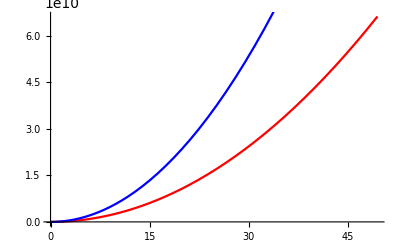

```mathematica
ListPlot[{ωAxis[data11]/taap[data11],-σPTX[data11,-310000]/taap[data11]//Im}//Transpose,Joined->True,PlotStyle->Red];
ListPlot[{ωAxis[data21]/taap[data21],-σPTX[data21,-10000]/taap[data21]//Im}//Transpose,Joined->True,PlotStyle->Blue];
Show[%%,%]
```

```mathematica
450/18.
8. π
```

25.

25.1327

Calculate the DC value numerically using ω = 0 case.

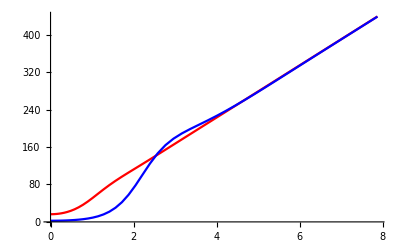

```mathematica
ListPlot[{ωAxis[data11]/(2π taap[data11]),-σPX[data11,-310000]/taap[data11]//Im}//Transpose,Joined->True,PlotStyle->Red];
ListPlot[{ωAxis[data21]/(2π taap[data21]),-σPX[data21,-3700000]/taap[data21]//Im}//Transpose,Joined->True,PlotStyle->Blue];
Show[%%,%]
```

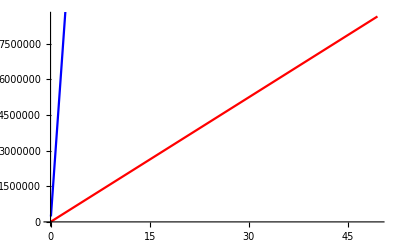

```mathematica
ListPlot[{ωAxis[data11]/taap[data11],-ρPX[data11,-310000]^-1/taap[data11]//Re}//Transpose,Joined->True,PlotStyle->Red];
ListPlot[{ωAxis[data21]/taap[data21],-ρPX[data21,-3700000]^-1/taap[data21]//Re}//Transpose,Joined->True,PlotStyle->Blue];
Show[%%,%]
```

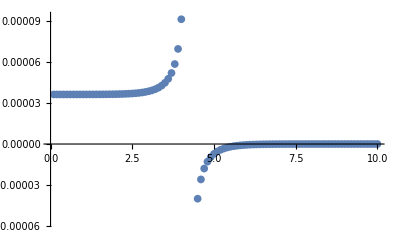

```mathematica
{Table[i/10,{i,1,100}],bSub[data11]^2/(w0[data11](w0[data11]-bSub[data11]^2 M5μ))/.M5μ->Table[10^(i/10),{i,1,100}]}//Transpose//N//ListPlot
```

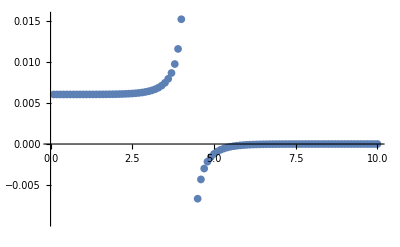

```mathematica
{Table[i/10,{i,1,100}],bSub[data11]/(w0[data11]-bSub[data11]^2 M5μ)/.M5μ->Table[10^(i/10),{i,1,100}]}//Transpose//N//ListPlot
```

```mathematica
30. 2π
%^2
```

188.496

35530.6

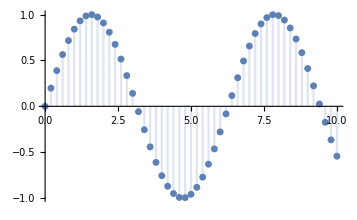

```mathematica
DiscretePlot[Sin[x],{x, 0, 10,0.2}]
```

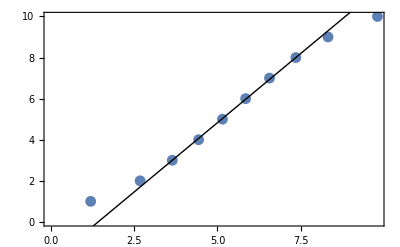

```mathematica
QuantilePlot[Range[10]]
```

### Combining function

```mathematica
name[data_]:="corrγSUSYμT"<>ToString[100 data⟦1,2⟧]<>"d100B"<>ToString[100data⟦1,3⟧]<>"d100"

dataMerge[data_,mdata_]:={data⟦1⟧,data⟦1⟧,mdata⟦2⟧,name[data]}/.data⟦1,-1⟧->mdata⟦1⟧
```

```mathematica
"corrγSUSYμT"<>ToString[100 data21⟦1,2⟧]<>"d100B"<>ToString[100data11⟦1,3⟧]<>"d100"
```

corrγSUSYμT1000d100B1d100

```mathematica
setDirectory[NotebookDirectory[]<>"M_derivative"]
save[,]
```

## test run σ, η

```mathematica
Quit[]
```

### Importing (data,μB)

```mathematica
SetDirectory[NotebookDirectory[]<>"f_data"];

data01=Get["corrγSUSYμT10d100B10000d10p6"];

data11=Get["corrγSUSYμT1B1d100"];
data12=Get["corrγSUSYμT1B34650d10p6"];
data13=Get["corrγSUSYμT1B25d100"];
data14=Get["corrγSUSYμT1B821600d10p6"];



data21=Get["corrγSUSYμT10B2886d10p6"];
data22=Get["corrγSUSYμT10B1d100"];
data23=Get["corrγSUSYμT10B72500d10p6"];
data24=Get["corrγSUSYμT10B25d100"];
```

### Thermodynamics

```mathematica
bSub[data_]:=data⟦1,3⟧
μSub[data_]:=data⟦1,2⟧
taap[data_]:=data⟦1,4⟧
entropy[data_]:=data⟦1,5⟧
w0[data_]:=data⟦1,6⟧+data⟦1,7⟧
all[data_]:=data⟦2⟧

ωgSize[data_]:=(data⟦2⟧//Dimensions)⟦1⟧
ωAxis[data_]:=(L+(1-Cos[(π #)/(2ωgSize[data]-1)])(U-L)&/@Range[0,ωgSize[data]-1])/.{L->10^-2,U->16π taap[data]}
```

### Constant BT finder

```mathematica
μSub[#]&/@{data01,data11,data12,data13,data14,data21,data22,data23,data24}//N
bSub[#]&/@{data01,data11,data12,data13,data14,data21,data22,data23,data24}//N
taap[#]&/@{data01,data11,data12,data13,data14,data21,data22,data23,data24}//N
bSub[#]/taap[#]^2&/@{data01,data11,data12,data13,data14,data21,data22,data23,data24}//N
```

{0.1,1.,1.,1.,1.,10.,10.,10.,10.}

{0.01,0.01,0.03465,0.25,0.8216,0.002886,0.01,0.0725,0.25}

{0.318255,0.313108,0.313094,0.312342,0.305017,0.168207,0.168207,0.16821,0.168245}

{0.0987302,0.102003,0.353471,2.56258,8.83106,0.102002,0.353436,2.56231,8.83198}

```mathematica
bSub[#]&/@{data11,data13,data21,data23}//N
bSub[#]/taap[#]^2&/@{data11,data13,data21,data23}//N
```

{0.01,0.25,0.002886,0.0725}

{0.102003,2.56258,0.102002,2.56231}

```mathematica
btFunc[data_]:=bSub[data]/taap[data]^2
rnsTemp[μ_]:=1/(4π)u'[z]/.u->Function[z,1-z^4+1/3 z^4(z^2-1)μ^2]/.z->1//Simplify
rnsMT[μ_]:=μ/rnsTemp[μ]
bTilde[μ_,B_]:=B/rnsTemp[μ]^2
```

```mathematica
Solve[μT==rnsMT[μ],μ]//Simplify;
bWhat=Solve[BT==bTilde[μ,B],B]/.%//Simplify//Flatten;
bFinder[data1_,data2_]:={μSub[data1],btFunc[data2],bWhat}/.{BT->btFunc[data2],μT->μSub[data1]}//N
```

```mathematica
bFinder[data11,data21]
bFinder[data12,data22]
bFinder[data21,data11]
bFinder[data22,data12]
```

{1.,0.102002,{B→0.00999994,B→37.4558}}

{1.,0.353436,{B→0.0346498,B→129.784}}

{10.,0.102003,{B→0.00288604,B→0.0129785}}

{10.,2.56258,{B→0.0725049,B→0.326055}}

### Kubo formula

σ and η are normalized already

Don’t normalize ρ and c’s. If affects the Kubo formula for c’s and η. 



### Try subtracting ω = 0 from each of the correlators. If not all at least ρPT.

#### σ

```mathematica
ρPX[data_,M5μ_]:=bSub[data]^2/(w0[data](w0[data]-bSub[data]^2 M5μ))(all[data]⟦All,3,3⟧)/ωAxis[data]
ρPTX[data_,M5μ_]:=-bSub[data]^2/(w0[data](w0[data]-bSub[data]^2 M5μ))(all[data]⟦All,3,4⟧)/ωAxis[data]

σPX[data_,M5μ_]:=-1/taap[data] 1/ρPX[data,M5μ]
σPTX[data_,M5μ_]:=-1/taap[data] 1/ρPTX[data,M5μ]
```

#### c

```mathematica
c8X[data_,M5μ_]:=bSub[data]/(w0[data]-bSub[data]^2 M5μ)(ρPX[data,M5μ] all[data]⟦All,3,6⟧+ρPTX[data,M5μ] all[data]⟦All,3,5⟧)/(ωAxis[data](ρPX[data,M5μ]^2+ρPTX[data,M5μ]^2)) 

c10TX[data_,M5μ_]:=bSub[data]/(w0[data]-bSub[data]^2 M5μ)(ρPX[data,M5μ] all[data]⟦All,3,5⟧-ρPTX[data,M5μ]all[data]⟦All,3,6⟧)/(ωAxis[data](ρPX[data,M5μ]^2+ρPTX[data,M5μ]^2)) 


c15X[data_,M5μ_]:=bSub[data]/w0[data](ρPX[data,M5μ] all[data]⟦All,6,3⟧+ρPTX[data,M5μ] all[data]⟦All,5,3⟧)/(ωAxis[data](ρPX[data,M5μ]^2+ρPTX[data,M5μ]^2))  
c17TX[data_,M5μ_]:=bSub[data]/w0[data](ρPX[data,M5μ] all[data]⟦All,5,3⟧-ρPTX[data,M5μ] all[data]⟦All,6,3⟧)/(ωAxis[data](ρPX[data,M5μ]^2+ρPTX[data,M5μ]^2))
```

#### η

```mathematica
ηPX[data_,M5μ_]:=(4π)/entropy[data]((all[data]⟦All,5,5⟧)/ωAxis[data] -(c8X[data,M5μ] c15X[data,M5μ]-c10TX[data,M5μ] c17TX[data,M5μ])ρPX[data,M5μ]+(c8X[data,M5μ] c17TX[data,M5μ]+c10TX[data,M5μ] c15X[data,M5μ])ρPTX[data,M5μ] )

ηPTX[data_,M5μ_]:=(4π)/entropy[data]((all[data]⟦All,5,6⟧)/ωAxis[data]-(c8X[data,M5μ] c17TX[data,M5μ]+c10TX[data,M5μ] c15X[data,M5μ])ρPX[data,M5μ]-(c8X[data,M5μ] c15X[data,M5μ]-c10TX[data,M5μ] c17TX[data,M5μ])ρPTX[data,M5μ])
```

```mathematica
ηPY[data_,M5μ_]:=(4π)/entropy[data](cof1(all[data]⟦All,5,5⟧)/ωAxis[data] -cof2(c8X[data,M5μ] c15X[data,M5μ]-c10TX[data,M5μ] c17TX[data,M5μ])ρPX[data,M5μ]+cof3(c8X[data,M5μ] c17TX[data,M5μ]+c10TX[data,M5μ] c15X[data,M5μ])ρPTX[data,M5μ] )
```

### Plot function (New)

```mathematica
pFunc[func_,ReIm_,data_,M5μ_,line_,color_,ωLow_:1,ωHigh_:-1,pRangeLow_:1,pRangeHigh_:-1]:=ListPlot[Transpose[{ωAxis[data]/(2π taap[data]),ReIm[func[data,M5μ]]}]⟦ωLow;;ωHigh⟧,PlotStyle->{line,color},Joined->True,InterpolationOrder->2] 

pRange[func_,ReIm_,data_,M5μ_,pRangeLow_:1,pRangeHigh_:-1]:={0.8Min[#],1.2Max[#]}&@ReIm[func[data,M5μ]]⟦pRangeLow;;pRangeHigh⟧

color=ColorData[97,"ColorList"];
```

### σ_DC Koreans

```mathematica
σDC=(2 π eE^2 T^2)/(-1 + 3 √(1 + 2/(3 π^2)μT^2))/.{T->taap[data11],μT->μSub[data11]}
```

0.29337088636338658064633258882367985601306940322559829214465 eE^2

```mathematica
σPX[data11,0]⟦1;;5⟧//Im//N
σPX[data21,0]⟦1;;5⟧//Im//N
```

{0.837506,0.833342,0.832267,0.833802,0.838217}

{0.366382,0.365496,0.365107,0.365772,0.367705}

### Plots

#### σ

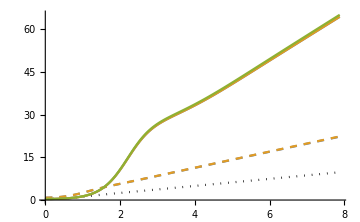

```mathematica
cutVal=-1;
M5μVal=0;
Show[
pFunc[σPX,Im,data01,M5μVal,Dotted,Black,1,cutVal],
pFunc[σPX,Im,data11,M5μVal,Dashed,color⟦1⟧,1,cutVal],
pFunc[σPX,Im,data12,M5μVal,Dashed,color⟦2⟧,1,cutVal],
pFunc[σPX,Im,data21,M5μVal,Automatic,color⟦1⟧,1,cutVal],
pFunc[σPX,Im,data22,M5μVal,Automatic,color⟦2⟧,1,cutVal],
pFunc[σPX,Im,data23,M5μVal,Automatic,color⟦3⟧,1,cutVal],
PlotRange->Automatic,ImageSize->Medium
]
```

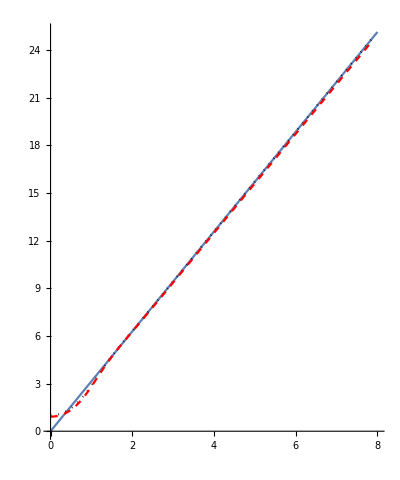
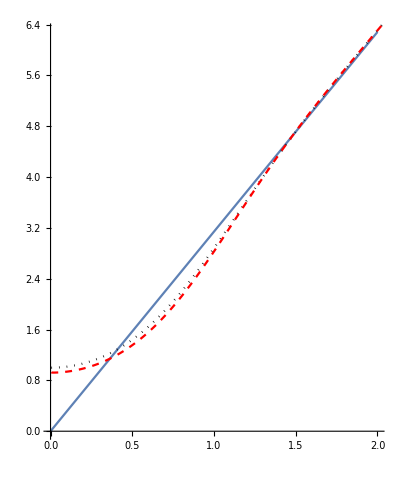
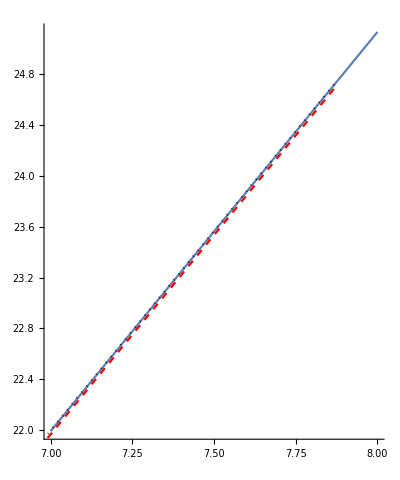

```mathematica
{Show[Plot[π ω,{ω,0,8}],pFunc[σPX,Im,data01,-1.63 10^4,Dotted,Black,1,cutVal],pFunc[σPX,Im,data11,-1.7 10^3,Dashed,Red,1,cutVal],AspectRatio->1.2],
Show[Plot[π ω,{ω,0,2}],pFunc[σPX,Im,data01,-1.63 10^4,Dotted,Black,1,cutVal],pFunc[σPX,Im,data11,-1.8 10^3,Dashed,Red,1,cutVal],AspectRatio->1.2],Show[Plot[π ω,{ω,7,8}],pFunc[σPX,Im,data01,-1.63 10^4,Dotted,Black,1,cutVal],pFunc[σPX,Im,data11,-1.8 10^3,Dashed,Red,1,cutVal],AspectRatio->1.2]}
```

#### σT

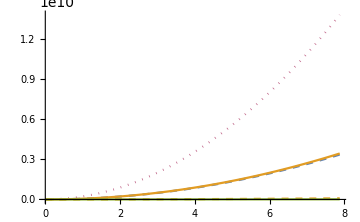

```mathematica
cutVal=-1;
M5μVal=0 10^5;
Show[
pFunc[σPTX,Im,data01,M5μVal,Dotted,color⟦-2⟧,1,cutVal],
pFunc[σPTX,Im,data11,M5μVal,Dashed,color⟦1⟧,1,cutVal],
pFunc[σPTX,Im,data12,M5μVal,Dashed,color⟦2⟧,1,cutVal],
(*pFunc[σPTX,Im,data21,M5μVal,Automatic,color⟦1⟧,1,cutVal],*)
pFunc[σPTX,Im,data22,M5μVal,Automatic,color⟦2⟧,1,cutVal],
pFunc[σPTX,Im,data23,M5μVal,Automatic,color⟦3⟧,1,cutVal],
PlotRange->Automatic,ImageSize->Medium
]
```

#### η

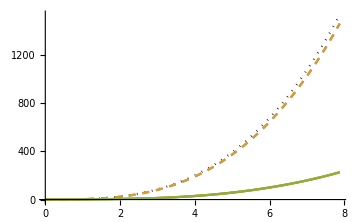

```mathematica
cutVal=-1;
M5μVal=0;
Show[
pFunc[ηPX,Im,data01,M5μVal,Dotted,Black,1,cutVal],
pFunc[ηPX,Im,data11,M5μVal,Dashed,color⟦1⟧,1,cutVal],
pFunc[ηPX,Im,data12,M5μVal,Dashed,color⟦2⟧,1,cutVal],
pFunc[ηPX,Im,data21,M5μVal,Automatic,color⟦1⟧,1,cutVal],
pFunc[ηPX,Im,data22,M5μVal,Automatic,color⟦2⟧,1,cutVal],
pFunc[ηPX,Im,data23,M5μVal,Automatic,color⟦3⟧,1,cutVal],
PlotRange->Automatic,ImageSize->Medium
]
```

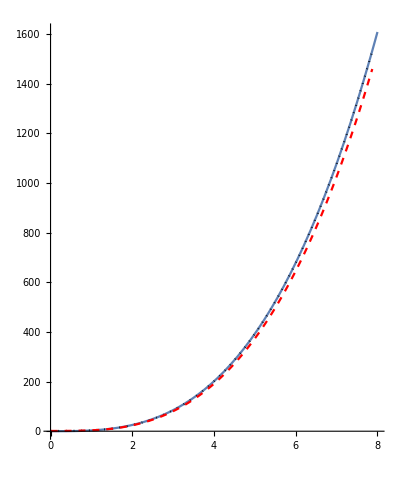
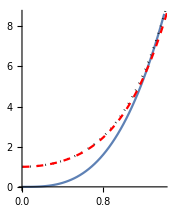
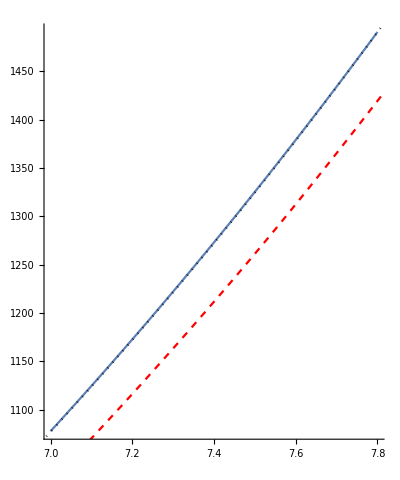

```mathematica
{Show[Plot[π ω^3,{ω,0,8}],pFunc[ηPX,Im,data01,-1.63 10^4,Dotted,Black,1,cutVal],pFunc[ηPX,Im,data11,-1.7 10^3,Dashed,Red,1,cutVal],AspectRatio->1.2],
Show[Plot[π ω^3,{ω,0,1.4}],pFunc[ηPX,Im,data01,-1.63 10^4,Dotted,Black,1,cutVal],pFunc[ηPX,Im,data11,-1.8 10^3,Dashed,Red,1,cutVal],AspectRatio->1.2],Show[Plot[π ω^3,{ω,7,7.8}],pFunc[ηPX,Im,data01,-1.63 10^4,Dotted,Black,1,cutVal],pFunc[ηPX,Im,data11,-1.8 10^3,Dashed,Red,1,cutVal],AspectRatio->1.2]}
```

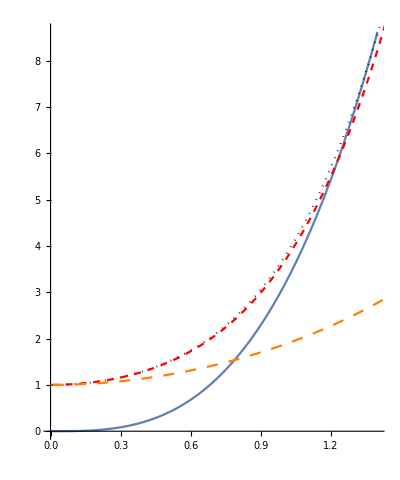

```mathematica
Show[Plot[π ω^3,{ω,0,1.4}],pFunc[ηPX,Im,data01,-1.63 10^4,Dotted,Black,1,cutVal],pFunc[ηPX,Im,data11,-1.8 10^3,Dashed,Red,1,cutVal],pFunc[ηPX,Im,data21,-1.8 10^3,Dashing[0.02],Orange,1,cutVal],AspectRatio->1.2]
```

Does it come back for the larger ω. I have data for large ω. I need to analyze it.

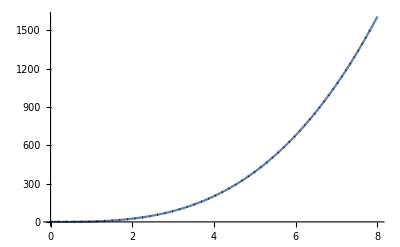

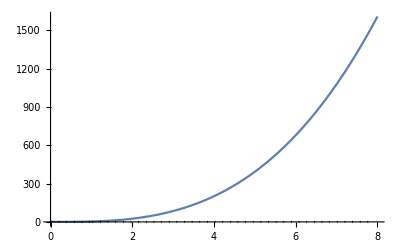

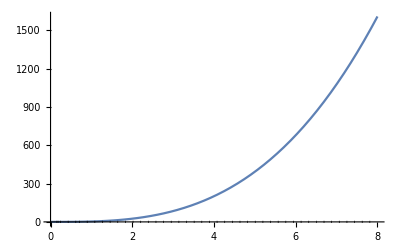

```mathematica
{cof1=1,cof2=0,cof3=0};Show[Plot[π ω^3,{ω,0,8}],pFunc[ηPY,Im,data01,0,Dotted,Black,1,cutVal]]
{cof1=0,cof2=1,cof3=0};Show[Plot[π ω^3,{ω,0,8}],pFunc[ηPY,Im,data01,0,Dotted,Black,1,cutVal]]
{cof1=0,cof2=0,cof3=1};Show[Plot[π ω^3,{ω,0,8}],pFunc[ηPY,Im,data01,0,Dotted,Black,1,cutVal]]
```

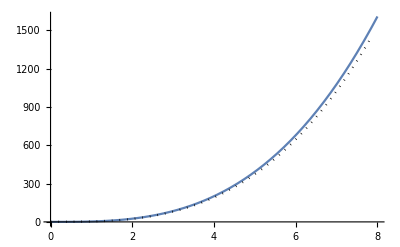

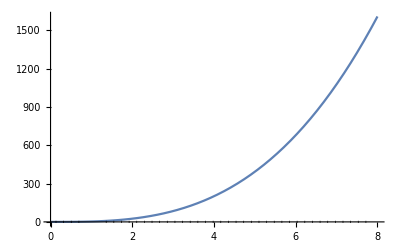

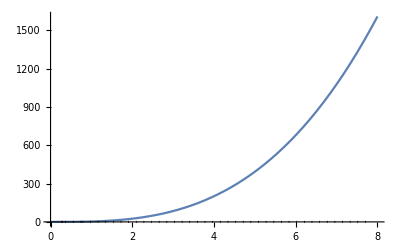

```mathematica
{cof1=1,cof2=0,cof3=0};Show[Plot[π ω^3,{ω,0,8}],pFunc[ηPY,Im,data11,0,Dotted,Black,1,cutVal]]
{cof1=0,cof2=1,cof3=0};Show[Plot[π ω^3,{ω,0,8}],pFunc[ηPY,Im,data11,0,Dotted,Black,1,cutVal]]
{cof1=0,cof2=0,cof3=1};Show[Plot[π ω^3,{ω,0,8}],pFunc[ηPY,Im,data11,0,Dotted,Black,1,cutVal]]
```

```mathematica
ηNorm[data_,M5μ_]:=bSub[data]^3/(w0[data](w0[data]-bSub[data]^2 M5μ)^2)
```

```mathematica
ηNorm[data01,-10^#]&/@Range[10]
```

{8.2869075313220819667666002125978532170616511078451614334184×10^-7,8.1485992472329780204029729351702860553212509289938197701057×10^-7,6.9371942926796017515083263838346733504370848364746135034694×10^-7,2.2062847797913172873465300614637138135109860168740894054826×10^-7,7.6779856391730505481560489739718144692070879561187897481189×10^-9,9.2018841011751446597340008472797362192258867670541573314602×10^-11,9.3787687437462912756253823425783644410319953262800265125179×10^-13,9.3967371889314438131843974490312524250191279546396942275095×10^-15,9.39853687297676456037345142550131405679262391168642407341×10^-17,9.3987168698168107012944364028585650922947991353566153116409×10^-19}

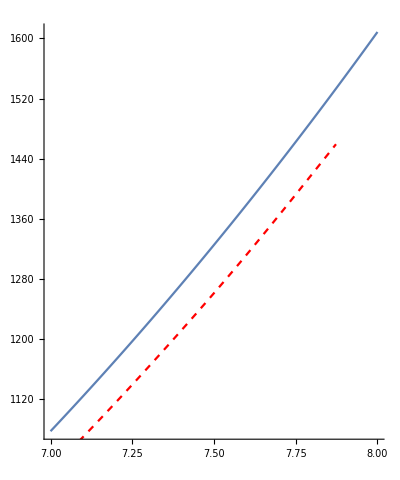
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Show[Plot[π ω^3,{ω,7,8}],pFunc[ηPX,Im,data11,10^#,Dashed,Red,1,cutVal],AspectRatio->1.2]&/@Range[-10,10]
```

```mathematica
Show[Plot[π ω^3,{ω,7,8}],pFunc[ηPX,Im,data11,ⅈ 10^#,Dashed,Red,1,cutVal],AspectRatio->1.2]&/@Range[-10,10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
μSub[]
```

{1/10,1,10}

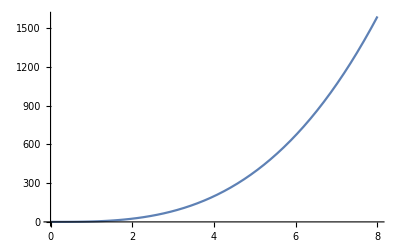
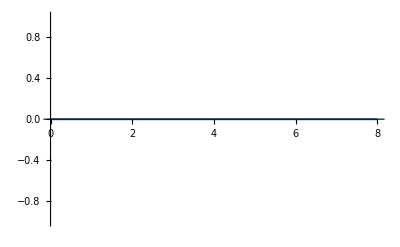
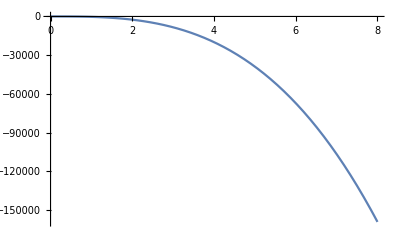

```mathematica
μSub[#]&/@{data01,data11,data21}
Plot[(1-μSub[#]^2)π ω^3,{ω,0,8}]&/@{data01,data11,data21}
```

#### ηT

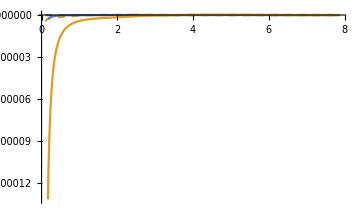

```mathematica
cutVal=-1;
M5μVal=0;
Show[
pFunc[ηPTX,Im,data11,M5μVal,Dashed,color⟦1⟧,1,cutVal],
pFunc[ηPTX,Im,data12,M5μVal,Dashed,color⟦2⟧,1,cutVal],
pFunc[ηPTX,Im,data21,M5μVal,Automatic,color⟦1⟧,1,cutVal],
pFunc[ηPTX,Im,data22,M5μVal,Automatic,color⟦2⟧,1,cutVal],
(*pFunc[ηPTX,Im,data23,M5μVal,Automatic,color⟦3⟧,1,cutVal],*)
PlotRange->Automatic,ImageSize->Medium
]
```

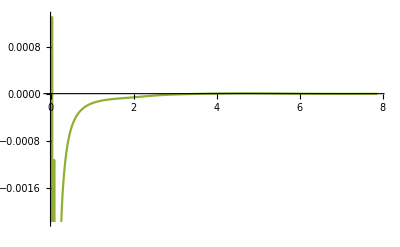

```mathematica
pFunc[ηPTX,Im,data23,M5μVal,Automatic,color⟦3⟧,1,cutVal]
```

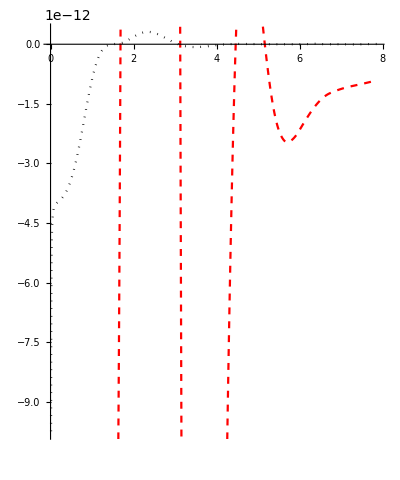
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{Show[pFunc[ηPTX,Im,data01,-1.63 10^4,Dotted,Black,1,cutVal],pFunc[ηPTX,Im,data11,-1.7 10^3,Dashed,Red,1,cutVal],AspectRatio->1.2],
Show[pFunc[ηPTX,Im,data01,-1.63 10^4,Dotted,Black,1,cutVal],pFunc[ηPTX,Im,data11,-1.8 10^3,Dashed,Red,1,cutVal],AspectRatio->1.2],
Show[pFunc[ηPTX,Im,data01,-1.63 10^4,Dotted,Black,1,cutVal],pFunc[ηPTX,Im,data11,-1.8 10^3,Dashed,Red,1,cutVal],AspectRatio->1.2]}
```

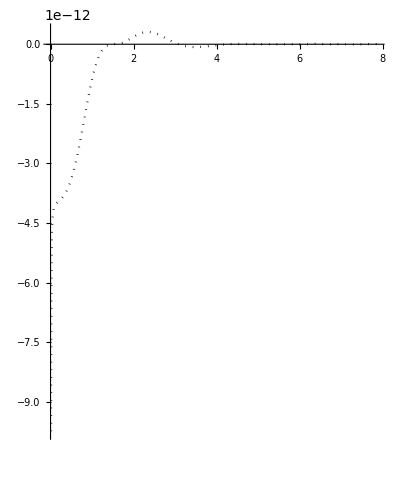

```mathematica
Show[pFunc[ηPTX,Im,data01,-1.63 10^4,Dotted,Black,1,cutVal],AspectRatio->1.2]
```

### Extra

```mathematica
σPTX[data11,0]⟦1⟧//N
```

-6.16564+1371.21 ⅈ

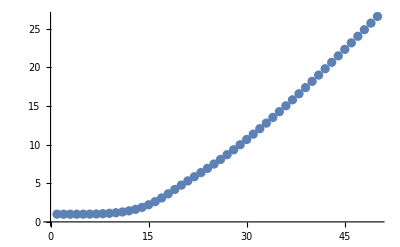
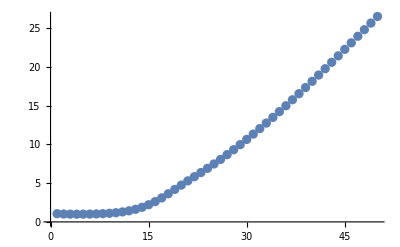
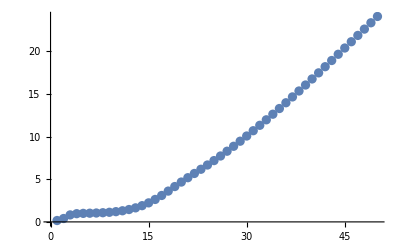
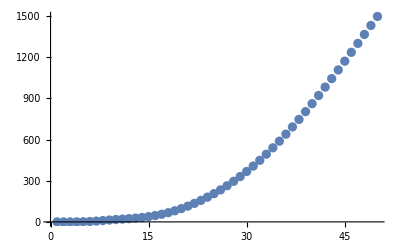
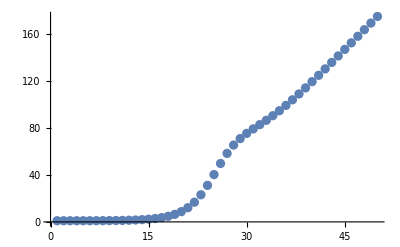
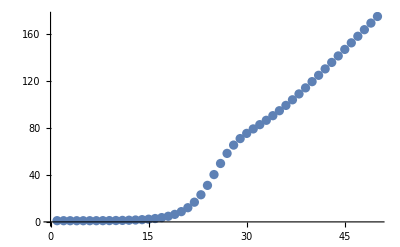
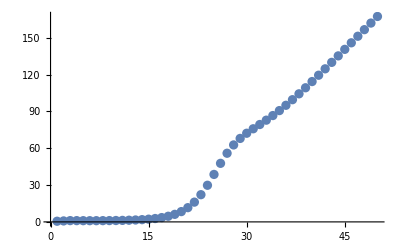
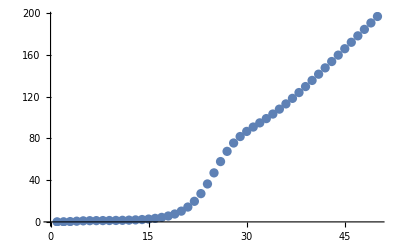

```mathematica
ListPlot[σPX[#,0]/(σPX[#,0]⟦5⟧//Im)//Im]&/@{data11,data12,data13,data14,data21,data22,data23,data24}
```

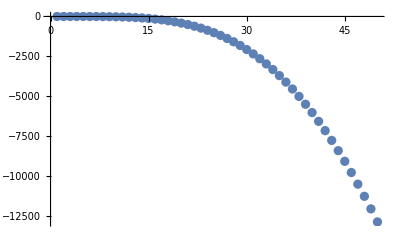
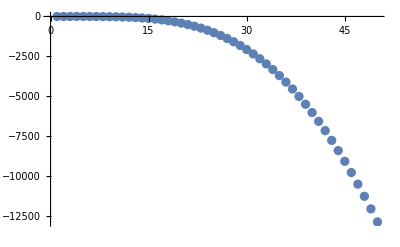
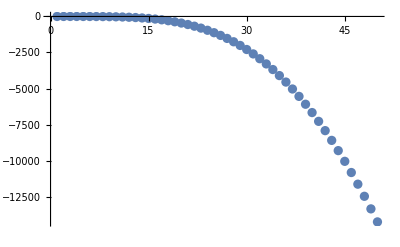
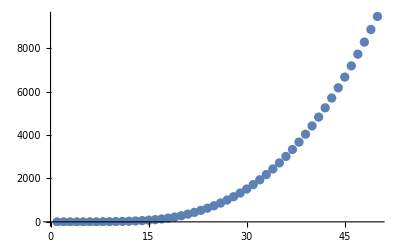
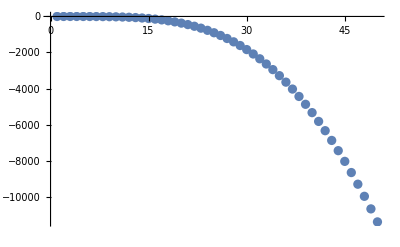
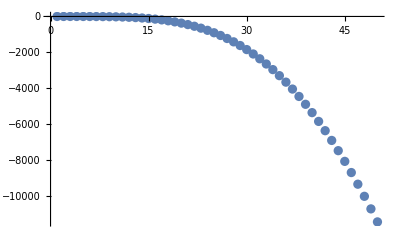
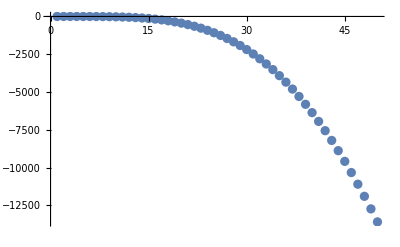
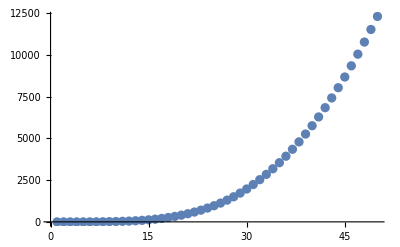

```mathematica
ListPlot[-σPTX[#,0]/(σPTX[#,0]⟦5⟧//Im)//Im]&/@{data11,data12,data13,data14,data21,data22,data23,data24}
```

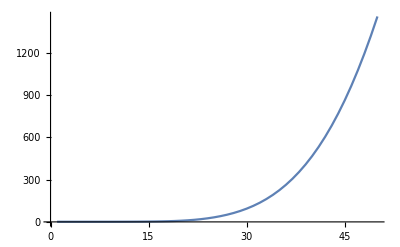
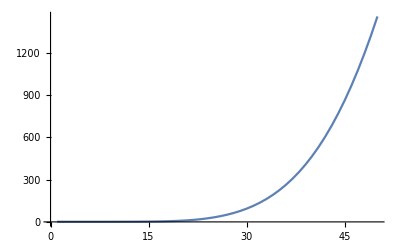
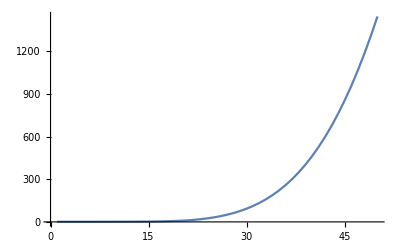
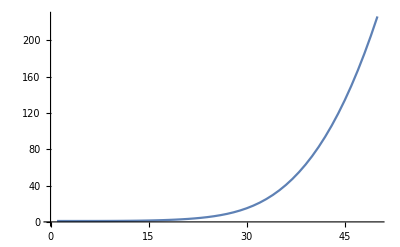
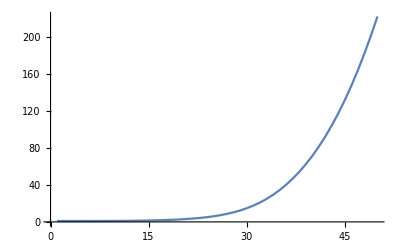
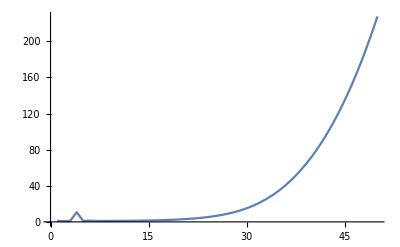
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListPlot[ηPX[#,0]/(ηPX[#,0]⟦1⟧//Im)//Im,Joined->True,InterpolationOrder->1,PlotRange->All]&/@{data11,data12,data13,data14,data21,data22,data23,data24}
```

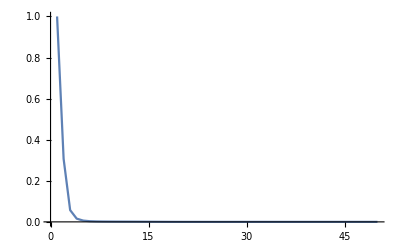
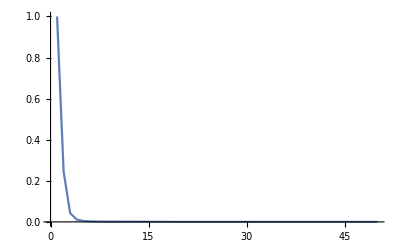
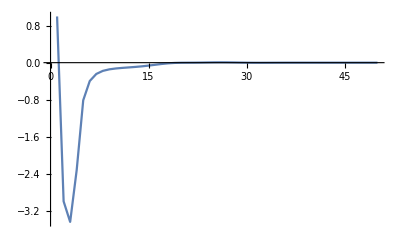
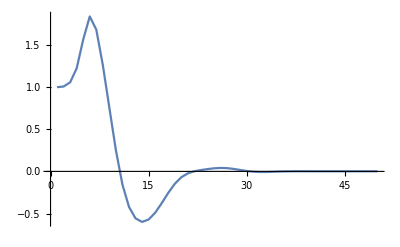
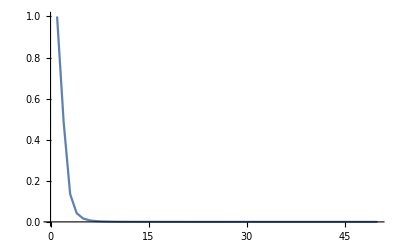
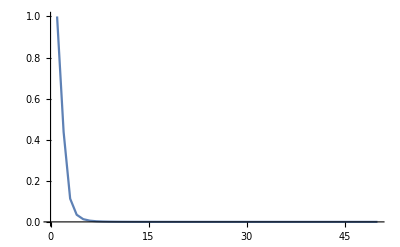
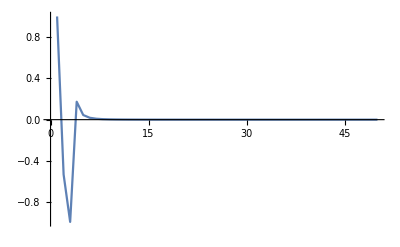
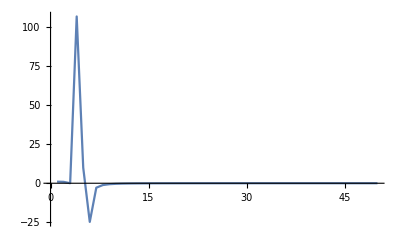

```mathematica
ListPlot[ηPTX[#,0]/(ηPTX[#,0]⟦1⟧//Im)//Im,Joined->True,InterpolationOrder->1,PlotRange->All]&/@{data11,data12,data13,data14,data21,data22,data23,data24}
```

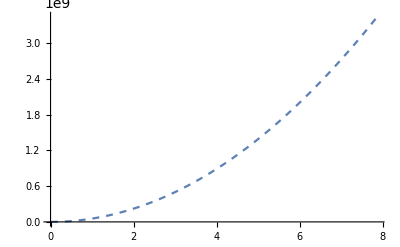
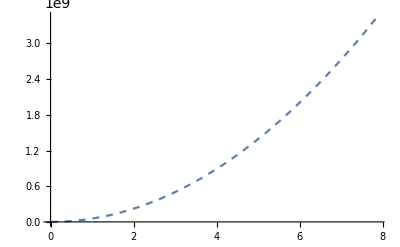
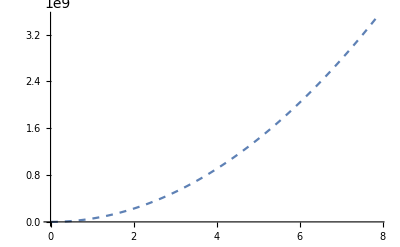
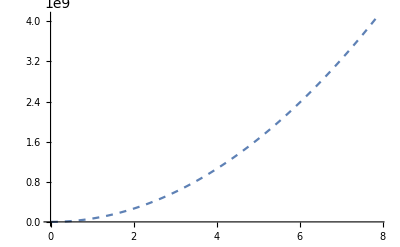
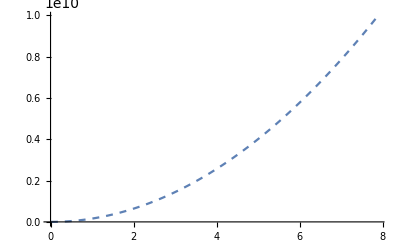
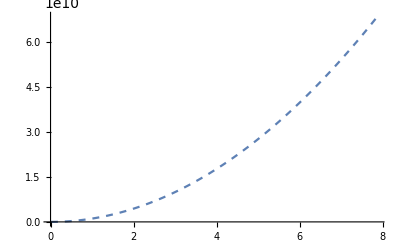
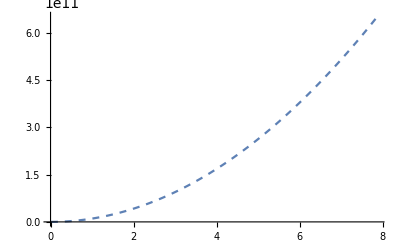
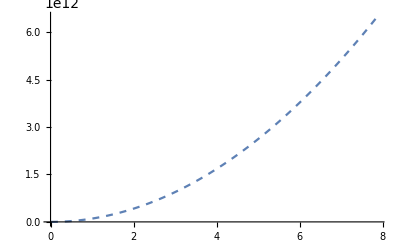
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
pFunc[σPTX,Im,data22,-10^#,Dashed,color⟦1⟧,1,cutVal]&/@Range[0,10]
```

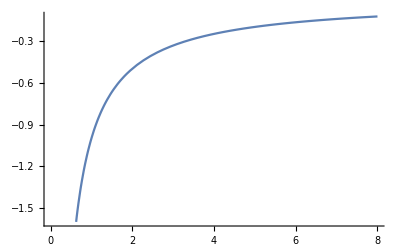

```mathematica
Plot[-ω^-1,{ω,0,8}]
```

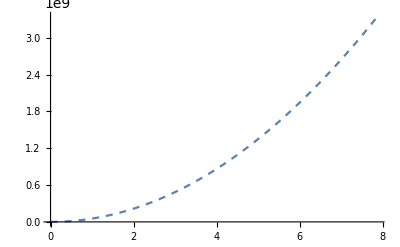
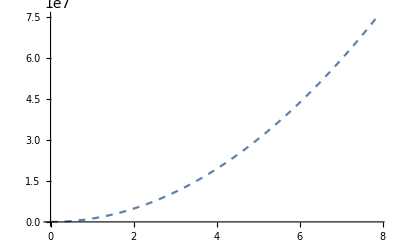
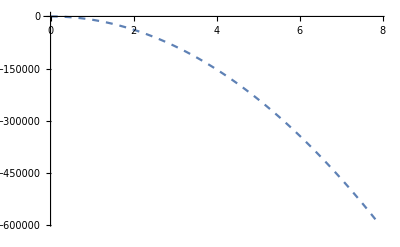
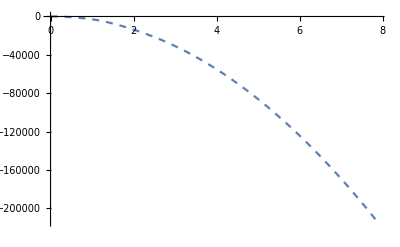
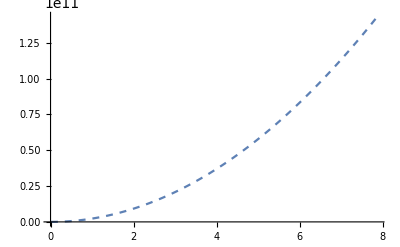
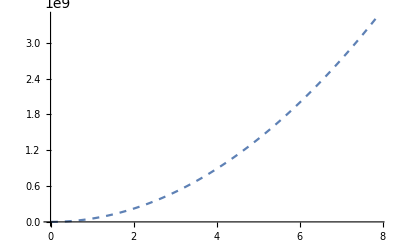
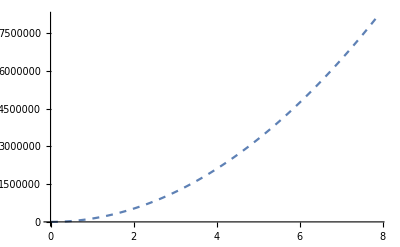
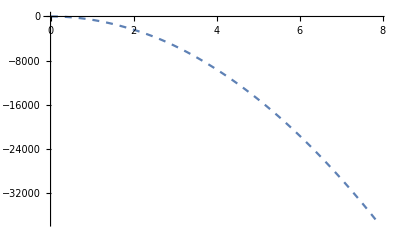

```mathematica
pFunc[σPTX,Im,#,M5μVal,Dashed,color⟦1⟧,1,cutVal]&/@{data11,data12,data13,data14,data21,data22,data23,data24}
```

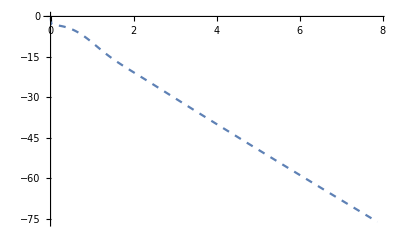

```mathematica
pFunc[σPX,Im,#,M5μVal,Dashed,color⟦1⟧,1,cutVal]&/@{data13}
```

```mathematica
pFunc[σPX,Im,data24,M5μVal,Automatic,color⟦4⟧,1,cutVal]
```

-Graphics-

## Older

### Testing

#### Numerical and analytical RN

```mathematica
data20=Get["corrγSUSYμT10B0d100"];
data20p=Get["1corrγSUSYμT10B0d100"];

data20-data20p/.μ->-1.6820725265684562//Flatten;
{Re[%]//ListPlot,Im[%]//ListPlot}
```

{-Graphics-,-Graphics-}

#### Same μ but different B

```mathematica
{Re[#]//ListPlot,Im[#]//ListPlot}&@(ρPX[data23]-ρPX[data24])
{Re[#]//ListPlot,Im[#]//ListPlot}&@(ρPTX[data23]-ρPTX[data24])
```

{-Graphics-,-Graphics-}

{-Graphics-,-Graphics-}

```mathematica
{Re[#]//ListPlot,Im[#]//ListPlot}&@(ρPX[data21]-ρPX[data22])
{Re[#]//ListPlot,Im[#]//ListPlot}&@(ρPTX[data21]-ρPTX[data22])
```

{-Graphics-,-Graphics-}

{-Graphics-,-Graphics-}

```mathematica
{Re[#]//ListPlot,Im[#]//ListPlot}&@(ηPX[data21]-ηPX[data22])
{Re[#]//ListPlot,Im[#]//ListPlot}&@(ηPTX[data21]-ηPTX[data22])
```

{-Graphics-,-Graphics-}

{-Graphics-,-Graphics-}

### Plot function

#### σ

```mathematica
pσ[data_,M5μ_,line_,color_,cut_:50]:=ListPlot[Transpose[{ωAxis[data]/(2π taap[data]),σPX[data,M5μ]//Im}]⟦;;cut⟧,PlotStyle->{line,color},Joined->True,InterpolationOrder->2,ImageSize->Small] 

pσT[data_,M5μ_,line_,color_,cut_:50]:=ListPlot[Transpose[{ωAxis[data]/(2π taap[data]),-σPTX[data,M5μ]//Im}]⟦;;cut⟧,PlotStyle->{line,color},Joined->True,InterpolationOrder->2,ImageSize->Small] 

rpσ[data_,M5μ_,line_,color_,cut_:50]:=ListPlot[Transpose[{ωAxis[data]/(2π taap[data]),-σPX[data,M5μ]//Re}]⟦;;cut⟧,PlotStyle->{line,color},Joined->True,InterpolationOrder->2,ImageSize->Small] 

rpσT[data_,M5μ_,line_,color_,cut_:50]:=ListPlot[Transpose[{ωAxis[data]/(2π taap[data]),σPTX[data,M5μ]//Re}]⟦;;cut⟧,PlotStyle->{line,color},Joined->True,InterpolationOrder->2,ImageSize->Small,PlotRange->All]
```

#### c

```mathematica
p8[data_,line_,color_,cut_:50]:=ListPlot[Transpose[{ωAxis[data]/(2π taap[data]),-c8X[data]/taap[data]^2//Im}]⟦;;cut⟧,PlotStyle->{line,color},Joined->True,InterpolationOrder->2,ImageSize->Small]

p10[data_,line_,color_,cut_:50]:=ListPlot[Transpose[{ωAxis[data]/(2π taap[data]),-c10TX[data]/taap[data]^2//Im}]⟦;;cut⟧,PlotStyle->{line,color},Joined->True,InterpolationOrder->2,ImageSize->Small]

p15[data_,line_,color_,cut_:50]:=ListPlot[Transpose[{ωAxis[data]/(2π taap[data]),-c15X[data]/taap[data]^2//Im}]⟦;;cut⟧,PlotStyle->{line,color},Joined->True,InterpolationOrder->2,ImageSize->Small]

p17[data_,line_,color_,cut_:50]:=ListPlot[Transpose[{ωAxis[data]/(2π taap[data]),-c17TX[data]/taap[data]^2//Im}]⟦;;cut⟧,PlotStyle->{line,color},Joined->True,InterpolationOrder->2,ImageSize->Small]
```

```mathematica
rp8[data_,line_,color_,cut_:50]:=ListPlot[Transpose[{ωAxis[data]/(2π taap[data]),-c8X[data]/taap[data]^2//Re}]⟦;;cut⟧,PlotStyle->{line,color},Joined->True,InterpolationOrder->2,ImageSize->Small]

rp10[data_,line_,color_,cut_:50]:=ListPlot[Transpose[{ωAxis[data]/(2π taap[data]),-c10TX[data]/taap[data]^2//Re}]⟦;;cut⟧,PlotStyle->{line,color},Joined->True,InterpolationOrder->2,ImageSize->Small]

rp15[data_,line_,color_,cut_:50]:=ListPlot[Transpose[{ωAxis[data]/(2π taap[data]),-c15X[data]/taap[data]^2//Re}]⟦;;cut⟧,PlotStyle->{line,color},Joined->True,InterpolationOrder->2,ImageSize->Small]

rp17[data_,line_,color_,cut_:50]:=ListPlot[Transpose[{ωAxis[data]/(2π taap[data]),-c17TX[data]/taap[data]^2//Re}]⟦;;cut⟧,PlotStyle->{line,color},Joined->True,InterpolationOrder->2,ImageSize->Small]
```

#### η

```mathematica
pη[data_,M5μ_,line_,color_,cut_:50]:=ListPlot[Transpose[{ωAxis[data]/(2π taap[data]),4π ηPX[data,M5μ]/entropy[data]//Im}]⟦;;cut⟧,PlotStyle->{line,color},Joined->True,InterpolationOrder->1,ImageSize->Small]

pηT[data_,M5μ_,line_,color_,cut_:50]:=ListPlot[Transpose[{ωAxis[data]/(2π taap[data]),4π ηPTX[data,M5μ]/entropy[data]//Im}]⟦;;cut⟧,PlotStyle->{line,color},Joined->True,InterpolationOrder->1,ImageSize->Small]

rpη[data_,M5μ_,line_,color_,cut_:50]:=ListPlot[Transpose[{ωAxis[data]/(2π taap[data]),-4π ηPX[data,M5μ]/entropy[data]//Re}]⟦;;cut⟧,PlotStyle->{line,color},Joined->True,InterpolationOrder->1,ImageSize->Small]

rpηT[data_,M5μ_,line_,color_,cut_:50]:=ListPlot[Transpose[{ωAxis[data]/(2π taap[data]),-4π ηPTX[data,M5μ]/entropy[data]//Re}]⟦;;cut⟧,PlotStyle->{line,color},Joined->True,InterpolationOrder->1,ImageSize->Small]
```

### Conformal limit

```mathematica
Show[pη[data21,Automatic,color⟦1⟧],Plot[π (bSub[data21]/taap[data21]^2 )^n ω^3/.{n->1},{ω,0,4},PlotStyle->{Dotted,Black}],ImageSize->Large]
```

-Graphics-

```mathematica
Show[pσ[data11,Automatic,color⟦1⟧],Plot[18π μSub[data11]^m(bSub[data11]/taap[data11]^2 )^n ω/.{m->1,n->1},{ω,0,4},PlotStyle->{Dotted,Black}],ImageSize->Small]
```

-Graphics-

```mathematica
Show[pσ[data21,Automatic,color⟦1⟧],Plot[1.5π μSub[data21]^m(bSub[data21]/taap[data21]^2 )^n ω/.{m->1,n->1/2},{ω,0,4},PlotStyle->{Dotted,Black}],ImageSize->Small]
```

-Graphics-

### Colors

```mathematica
ColorData[#,"ColorList"]&/@Range[100]//TableForm
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  |

```mathematica
ColorData[#,"ColorList"]&/@Range[100,113]//TableForm
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

### Conductivity

Dashed => 			μ = 1
Solid ==> 			μ = 10

Make an inset to show the small ω behavior from ω = [0,1]

At B = 0, the Kubo relations are useless.

```mathematica
cutVal=50;
M5μVal=0;
color=ColorData[97,"ColorList"];
```

```mathematica
pFunc[σPX,Im,#,M5μVal,Dashed,color⟦1⟧,1,cutVal]&/@{data11,data12,data13,data14,data21,data22,data23,data24}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
pσ[#,M5μVal,Dashed,color⟦1⟧,cutVal]&/@{data11,data12,data13,data14,data21,data22,data23,data24}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
σPlot1=Show[
pσ[data11,M5μVal,Dashed,color⟦1⟧,cutVal],
pσ[data12,M5μVal,Dashed,color⟦2⟧,cutVal],
pσ[data13,M5μVal,Dashed,color⟦3⟧,cutVal],
pσ[data14,M5μVal,Dashed,color⟦4⟧,cutVal],
pσ[data21,M5μVal,Automatic,color⟦1⟧,cutVal],
pσ[data22,M5μVal,Automatic,color⟦2⟧,cutVal],
pσ[data23,M5μVal,Automatic,color⟦3⟧,cutVal],
pσ[data24,M5μVal,Automatic,color⟦4⟧,cutVal],
PlotRange->{0,12},ImageSize->Large
]
```

-Graphics-

```mathematica
μSub[#]&/@{data11,data21}//N
bSub[#]/taap[#]^2&/@{data11,data12,data13,data14}//N
```

{1.,10.}

{0.102003,0.353471,2.56258,8.83106}

```mathematica
σPlot2=Show[
pσ[data11,Dashed,color⟦1⟧],pσ[data12,Dashed,color⟦2⟧],pσ[data13,Dashed,color⟦3⟧],(*pσ[data14,Dashed,color⟦4⟧],*)
pσ[data21,Automatic,color⟦1⟧],pσ[data22,Automatic,color⟦2⟧],pσ[data23,Automatic,color⟦3⟧],pσ[data24,Automatic,color⟦4⟧],
PlotRange->All,ImageSize->Large,AxesLabel->{Style["ω/(2  π T)",15],Style["(σ_⊥)/T",15]}
]
```

-Graphics-

```mathematica
pσT[data21,Automatic,color⟦1⟧]
```

-Graphics-

```mathematica
Show[
pσT[data11,Dashed,color⟦1⟧],pσT[data12,Dashed,color⟦2⟧],
(*pσT[data21,Automatic,color⟦1⟧],*)pσT[data22,Automatic,color⟦2⟧],pσT[data23,Automatic,color⟦3⟧],pσT[data24,Automatic,color⟦4⟧],
PlotRange->All,ImageSize->Large,AxesLabel->{Style["ω/(4  π T)",15],Style["((σ̃)_⊥)/T",15]}
]
```

-Graphics-

```mathematica
Show[
rpσ[data11,Dashed,color⟦1⟧],rpσ[data12,Dashed,color⟦2⟧],
rpσ[data21,Automatic,color⟦1⟧],rpσ[data22,Automatic,color⟦2⟧],rpσ[data23,Automatic,color⟦3⟧],rpσ[data24,Automatic,color⟦4⟧],
PlotRange->All,ImageSize->Large,AxesLabel->{Style["ω/(4  π T)",15],Style["Im[SubscriptBox[σ, ⊥]]/T",15]}
]
```

-Graphics-

```mathematica
Show[
rpσT[data11,Dashed,color⟦1⟧],rpσT[data12,Dashed,color⟦2⟧],
rpσT[data21,Automatic,color⟦1⟧],rpσT[data22,Automatic,color⟦2⟧],rpσT[data23,Automatic,color⟦3⟧],rpσT[data24,Automatic,color⟦4⟧],
PlotRange->All,ImageSize->Large,AxesLabel->{Style["ω/(4  π T)",15],Style["Im[SubscriptBox[OverscriptBox[σ, ~], ⊥]]/T",15]}
]
```

-Graphics-

### c_8, c_10, c_15, c_17

#### Graphics: Im[...]

```mathematica
{p8[data00],p8[data10]}
{p8[data01],p8[data11]}
```

{-Graphics-,-Graphics-}

{-Graphics-,-Graphics-}

```mathematica
{p10[data00],p10[data10]}
{p10[data01],p10[data11]}
```

{-Graphics-,-Graphics-}

{-Graphics-,-Graphics-}

```mathematica
{p15[data00],p15[data10]}
{p15[data01],p15[data11]}
```

{-Graphics-,-Graphics-}

{-Graphics-,-Graphics-}

```mathematica
{p17[data00],p17[data10]}
{p17[data01],p17[data11]}
```

{-Graphics-,-Graphics-}

{-Graphics-,-Graphics-}

#### Graphics: Re[...]

```mathematica
{rp8[data00],rp8[data10]}
{rp8[data01],rp8[data11]}
```

{-Graphics-,-Graphics-}

{-Graphics-,-Graphics-}

```mathematica
{rp10[data00],rp10[data10]}
{rp10[data01],rp10[data11]}
```

{-Graphics-,-Graphics-}

{-Graphics-,-Graphics-}

```mathematica
{rp15[data00],rp15[data10]}
{rp15[data01],rp15[data11]}
```

{-Graphics-,-Graphics-}

{-Graphics-,-Graphics-}

```mathematica
{rp17[data00],rp17[data10]}
{rp17[data01],rp17[data11]}
```

{-Graphics-,-Graphics-}

{-Graphics-,-Graphics-}

### Shear viscosity

```mathematica
cutVal=12;
```

```mathematica
1/(4π)//N
```

0.0795775

```mathematica
Show[
pη[data11,Dashed,color⟦1⟧,cutVal],pη[data12,Dashed,color⟦2⟧,cutVal],pη[data13,Dashed,color⟦3⟧,cutVal],pη[data14,Dashed,color⟦4⟧,cutVal],
pη[data21,Solid,color⟦1⟧,cutVal],pη[data22,Solid,color⟦2⟧,cutVal],pη[data23,Solid,color⟦3⟧,cutVal],pη[data24,Solid,color⟦4⟧,cutVal],
PlotRange->All,ImageSize->Large
]
```

-Graphics-

```mathematica
Show[
pη[data11,-30000,Dashed,color⟦1⟧],pη[data12,0,Dashed,color⟦2⟧],pη[data13,0,Dashed,color⟦3⟧],pη[data14,0,Dashed,color⟦4⟧],
pη[data21,0,Solid,color⟦1⟧],pη[data22,0,Solid,color⟦2⟧],pη[data23,0,Solid,color⟦3⟧],pη[data24,0,Solid,color⟦4⟧],
PlotRange->All,ImageSize->Large,AxesLabel->{Style["ω/(4  π T)",15],Style["(η_(||))/s",15]}
]
```

-Graphics-

-Graphics-

```mathematica
cutVal=20;
Show[
pηT[data11,Dashed,color⟦1⟧,cutVal],pηT[data12,Dashed,color⟦2⟧,cutVal],
pηT[data21,Automatic,color⟦1⟧,cutVal],pηT[data22,Automatic,color⟦2⟧,cutVal],pηT[data23,Automatic,color⟦3⟧,cutVal],(*pηT[data24,Automatic,color⟦4⟧,cutVal],*)
PlotRange->All,ImageSize->Large
]
```

-Graphics-

```mathematica
{pηT[data11,Dashed,color⟦1⟧,cutVal],pηT[data12,Dashed,color⟦2⟧,cutVal],
pηT[data21,Automatic,color⟦1⟧,cutVal],pηT[data22,Automatic,color⟦2⟧,cutVal],pηT[data23,Automatic,color⟦3⟧,cutVal],pηT[data24,Automatic,color⟦4⟧,cutVal]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Show[
pηT[data11,Dashed,color⟦1⟧],pηT[data12,Dashed,color⟦2⟧],
pηT[data21,Automatic,color⟦1⟧],pηT[data22,Automatic,color⟦2⟧],pηT[data23,Automatic,color⟦3⟧],pηT[data24,Automatic,color⟦4⟧],
PlotRange->All,ImageSize->Large,AxesLabel->{Style["ω/(4  π T)",15],Style["((η̃)_⊥)/T",15]}
]
```

-Graphics-

```mathematica
Show[
rpη[data11,Dashed,color⟦1⟧],rpη[data12,Dashed,color⟦2⟧],
rpη[data21,Automatic,color⟦1⟧],rpη[data22,Automatic,color⟦2⟧],rpη[data23,Automatic,color⟦3⟧],rpη[data24,Automatic,color⟦4⟧],
PlotRange->All,ImageSize->Large,AxesLabel->{Style["ω/(4  π T)",15],Style["Im[SubscriptBox[η, ⊥]]/T",15]}
]
```

-Graphics-

```mathematica
Show[
rpηT[data11,Dashed,color⟦1⟧],rpηT[data12,Dashed,color⟦2⟧],
rpηT[data21,Automatic,color⟦1⟧],rpηT[data22,Automatic,color⟦2⟧],rpηT[data23,Automatic,color⟦3⟧],rpηT[data24,Automatic,color⟦4⟧],
PlotRange->All,ImageSize->Large,AxesLabel->{Style["ω/(4  π T)",15],Style["Im[SubscriptBox[OverscriptBox[η, ~], ⊥]]/T",15]}
]
```

-Graphics-

### Detailing

Thinking of σ, B, μ phase diagram

```mathematica
cutVal=10;
color=ColorData[97,"ColorList"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{pσ[data01,Dashed,color⟦1⟧]}
{pσ[data11,Dashed,color⟦1⟧],pσ[data12,Dashed,color⟦2⟧],pσ[data13,Dashed,color⟦3⟧],pσ[data14,Dashed,color⟦4⟧]}
{pσ[data21,liquid,color⟦1⟧],pσ[data22,Solid,color⟦2⟧],pσ[data23,Solid,color⟦3⟧],pσ[data24,Solid,color⟦4⟧]}
```

{-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{Show[pσ[data01,Dashed,color⟦1⟧],pσ[data11,Solid,color⟦1⟧],pσ[data12,Solid,color⟦2⟧]],Show[pσ[data21,Solid,color⟦1⟧],pσ[data22,Solid,color⟦2⟧],pσ[data23,Solid,color⟦3⟧]]}
```

{-Graphics-,-Graphics-}

```mathematica
cutVal=35;
{pσ[data01,Dashed,color⟦1⟧,cutVal],Show[pσ[data11,Solid,color⟦1⟧,cutVal],pσ[data12,Solid,color⟦2⟧,cutVal]],Show[pσ[data21,Solid,color⟦1⟧,cutVal],pσ[data22,Solid,color⟦2⟧,cutVal],pσ[data23,Solid,color⟦3⟧,cutVal]]}
```

{-Graphics-,-Graphics-,-Graphics-}

Consider making less variation on μ and B for the plot of σT

```mathematica
μSub[#]&/@{data11,data21}//N
bSub[#]/taap[#]^2&/@{data11,data12,data13,data14}//N
```

{1.,10.}

{0.102003,0.353471,2.56258,8.83106}

```mathematica
pσT[data01,Dashed,color⟦1⟧]
{pσT[data11,Dashed,color⟦1⟧],pσT[data12,Dashed,color⟦2⟧],pσT[data13,Dashed,color⟦3⟧],pσT[data14,Dashed,color⟦4⟧]}
{pσT[data21,Solid,color⟦1⟧],pσT[data22,Solid,color⟦2⟧],pσT[data23,Solid,color⟦3⟧],pσT[data24,Solid,color⟦4⟧]}
```

-Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
pη[data01,Dashed,color⟦1⟧]
{pη[data11,Dashed,color⟦1⟧],pη[data12,Dashed,color⟦2⟧],pη[data13,Dashed,color⟦3⟧],pη[data14,Dashed,color⟦4⟧]}
{pη[data21,Solid,color⟦1⟧],pη[data22,Solid,color⟦2⟧],pη[data23,Solid,color⟦3⟧],pη[data24,Solid,color⟦4⟧]}
```

-Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
cutVal=20;
pσ[0.5data01,Dashed,color⟦1⟧,cutVal]
```

-Graphics-

```mathematica
cutVal=20;
pσ[data01,Dashed,color⟦1⟧,cutVal]
{pη[data11,Dashed,color⟦1⟧,cutVal],pη[data12,Dashed,color⟦2⟧,cutVal],pη[data13,Dashed,color⟦3⟧,cutVal],pη[data14,Dashed,color⟦4⟧,cutVal]}
{pη[data21,Solid,color⟦1⟧,cutVal],pη[data22,Solid,color⟦2⟧,cutVal],pη[data23,Solid,color⟦3⟧,cutVal],pη[data24,Solid,color⟦4⟧,cutVal]}
```

-Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Show[pη[data11,Dashed,color⟦1⟧],Plot[24 ω^3,{ω,0,4},PlotStyle->Red]]
```

-Graphics-

```mathematica
Show[pη[data21,Dashed,color⟦1⟧],Plot[3.7 ω^3,{ω,0,4},PlotStyle->Red]]
```

-Graphics-

```mathematica
Show[pη[data14,Dashed,color⟦1⟧],Plot[24 ω^3,{ω,0,4},PlotStyle->Red]]
```

-Graphics-

```mathematica
Show[pη[data24,Dashed,color⟦1⟧],Plot[3.7 ω^3,{ω,0,4},PlotStyle->Red]]
```

-Graphics-

```mathematica
3.7/π
%^-1
```

1.17775

0.849079

```mathematica
(√3)/2//N
```

0.866025

```mathematica
3.7/π 10bSub[data21]//N
1/%
```

0.0339898

29.4206

```mathematica
1/√2//N
```

0.707107

```mathematica
{Show[pη[data11,Dashed,color⟦1⟧,cutVal],pη[data12,Dashed,color⟦2⟧,cutVal],pη[data13,Dashed,color⟦3⟧,cutVal],pη[data14,Dashed,color⟦4⟧,cutVal]],
Show[pη[data21,Solid,color⟦1⟧,cutVal],pη[data22,Solid,color⟦2⟧,cutVal],pη[data23,Solid,color⟦3⟧,cutVal],pη[data24,Solid,color⟦4⟧,cutVal]]}
```

{-Graphics-,-Graphics-}

```mathematica
{pηT[data11,Dashed,color⟦1⟧],pηT[data12,Dashed,color⟦2⟧],pηT[data13,Dashed,color⟦3⟧],pηT[data14,Dashed,color⟦4⟧]}
{pηT[data21,Solid,color⟦1⟧],pηT[data22,Solid,color⟦2⟧],pηT[data23,Solid,color⟦3⟧],pηT[data24,Solid,color⟦4⟧]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{pηT[data11,Dashed,color⟦1⟧,cutVal],pηT[data12,Dashed,color⟦2⟧,cutVal],pηT[data13,Dashed,color⟦3⟧,cutVal],pηT[data14,Dashed,color⟦4⟧,cutVal]}
{pηT[data21,Solid,color⟦1⟧,cutVal],pηT[data22,Solid,color⟦2⟧,cutVal],pηT[data23,Solid,color⟦3⟧,cutVal],pηT[data24,Solid,color⟦4⟧,cutVal]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Which M5μ?

### σ

```mathematica
pFunc[σPX,Im,data11,-(1+0ⅈ)10^#,Dashed,color⟦1⟧]&/@Range[10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
pFunc[σPX,Im,data11,(1-0ⅈ)10^#,Dashed,color⟦1⟧]&/@Range[10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
pFunc[σPX,Im,data11,# 10^2,Dashed,color⟦1⟧]&/@Range[10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Show[Plot[π ω,{ω,0,8},PlotStyle->Black],pFunc[σPX,Im,data11,-1.8 10^3,Dashed,color⟦4⟧],ImageSize->Large]
```

-Graphics-

```mathematica
Show[
pFunc[σPX,Im,data11,-1.8 10^3,Dashed,color⟦1⟧,1,43],
pFunc[σPX,Im,data21,3.92 10^5,Dotted,color⟦2⟧,1,43],
Plot[π ω,{ω,0,6.1},PlotStyle->{Thin,Black}],
ImageSize->Large]
```

-Graphics-

```mathematica
pFunc[σPX,Im,data11,-3.92 10^5,Dashed,color⟦1⟧]
```

-Graphics-

```mathematica
Show[Plot[π ω,{ω,0,8},PlotStyle->Black],pFunc[σPX,Im,data11,3.92 10^5,Dashed,color⟦1⟧],ImageSize->Large]
```

-Graphics-

```mathematica
4 10^5 B δμ/.{B->1,δμ->10^-10}//N
```

0.00004

### η

```mathematica
pFunc[ηPX,Im,data11,-(1+0ⅈ)10^#,Dashed,color⟦1⟧]&/@Range[10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
pFunc[ηPX,Im,data11,(1+0ⅈ)10^#,Dashed,color⟦1⟧]&/@Range[10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
pFunc[ηPX,Im,data21,-(1+0ⅈ)10^#,Dashed,color⟦1⟧]&/@Range[10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
pFunc[ηPX,Im,data21,(1+0ⅈ)10^#,Dashed,color⟦1⟧]&/@Range[10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Plot[π ω^3,{ω,0,8},PlotStyle->Black,GridLines->Automatic,AspectRatio->1.2,Frame->True]
```

-Graphics-

```mathematica
Show[Plot[π ω^3,{ω,0,8},PlotStyle->Black],pFunc[ηPX,Im,data11,-10^#,Dashed,color⟦4⟧],ImageSize->Small]&/@Range[10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Extra

```mathematica
prec1=60;
```

```mathematica
δμkZ[delM_,μk0_,μkZ_,δμkZ_,Δμ_:10^-10]:=SetPrecision[(μkZ-δμkZ-μk0)⟦2⟧ -(1 + ⅈ)bSub[μk0]Δμ (delM+RandomReal[{10^2,10^3}]) ,60]
```

```mathematica
δμkZ[3.92 10^5,data11,data12,data01]//Dimensions
```

{50,6,6}